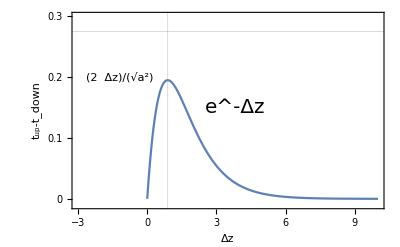

```mathematica
Show[{Plot[(√2 z)/(√(2.5^2+z^2))Exp[-z],{z,0,10},PlotRange->{{-3,10},{-0.01,0.3}},Axes->False,Frame->True,FrameTicksStyle->Directive[FontSize->20],FrameTicks->{{{0,0.1,0.2,0.3},None},{Automatic,None}},FrameLabel->{{Style["t_up-t_down",FontSize->20],None},{Style["Δz",FontSize->20],None}},GridLines->{{0.8879736439705752},{0.275}}],Graphics[Text["(2  Δz)/(√(a^2))",{-1.2,0.2}]],Graphics[Text[Style["e^-Δz",FontSize->20],{3.8,0.15}]]}]
```

```mathematica
sorbital=Table[(1/(32 Pi a^3))^(1/2)(2-(√(x^2+y^2+z^2))/a)Exp[-√(x^2+y^2+z^2)/(2a)],{x,-10,10,2},{y,-10,10,2},{z,-10,10,2}];
```

```mathematica
Integrate[-2 d ⅇ^(-1/2 √(x^2+y^2+(d-z)^2)-1/2 √(x^2+y^2+z^2)),{x,-Infinity,Infinity},{y,-Infinity,Infinity},{z,-Infinity,Infinity}]
```

Refine::cas: Warning: contradictory assumption(s) x∈Reals&&y∈Reals&&(x≠0||y≠0)&&(√(-x^2-y^2)≠0||√(-x^2-y^2)∉Reals)&&Re[a]>0 encountered.

General::stop: Further output of Refine::cas will be suppressed during this calculation.

```mathematica
(1/(32 Pi))^(1/2)(z-d)Exp[-√(x^2+y^2+(z-d)^2)/(2)]*(1/(32 Pi))^(1/2)(2-√(x^2+y^2+z^2))Exp[-√(x^2+y^2+z^2)/(2 )]//FullSimplify
```

```mathematica
32 π
```

```mathematica
ⅇ^(1/2 (-√(x^2+y^2+(d-z)^2)-√(x^2+y^2+z^2))) (d-z) (-2+√(x^2+y^2+z^2))//Expand
```

-2 d ⅇ^(-1/2 √(x^2+y^2+(d-z)^2)-1/2 √(x^2+y^2+z^2))+2 ⅇ^(-1/2 √(x^2+y^2+(d-z)^2)-1/2 √(x^2+y^2+z^2)) z+d ⅇ^(-1/2 √(x^2+y^2+(d-z)^2)-1/2 √(x^2+y^2+z^2)) √(x^2+y^2+z^2)-ⅇ^(-1/2 √(x^2+y^2+(d-z)^2)-1/2 √(x^2+y^2+z^2)) z √(x^2+y^2+z^2)

```mathematica
Integrate[ⅇ^(-1/2 √(x^2+y^2+z^2-2z d+d^2)-1/2 √(x^2+y^2+z^2)),{x,-Infinity,Infinity},{y,-Infinity,Infinity},{z,-Infinity,Infinity}]
```

64 π

```mathematica
Normal[Series[ⅇ^(-1/2 √(x^2+y^2+(d-z)^2)-1/2 √(x^2+y^2+z^2)),{x,0,1},{y,0,1},{z,0,1}]]
```

ⅇ^(-(√(d^2))/2)+(-1/2 ⅇ^(-(√(d^2))/2)+(√(d^2) ⅇ^(-(√(d^2))/2))/(2 d)) z

```mathematica
Clear[a]
D[(√2 z)/(√(a^2+z^2))Exp[-z],z]
```

-(√2 ⅇ^-z z^2)/((a^2+z^2)^(3/2))+(√2 ⅇ^-z)/(√(a^2+z^2))-(√2 ⅇ^-z z)/(√(a^2+z^2))

```mathematica
Solve[-(√2 ⅇ^-z z^2)/((a^2+z^2)^(3/2))+(√2 ⅇ^-z)/(√(a^2+z^2))-(√2 ⅇ^-z z)/(√(a^2+z^2))==0,z]
```

{{z→-((2/3)^(1/3) a^2)/((9 a^2+√3 √(27 a^4+4 a^6))^(1/3))+((9 a^2+√3 √(27 a^4+4 a^6))^(1/3))/(2^(1/3) 3^(2/3))},{z→((1+ⅈ √3) a^2)/(2^(2/3) 3^(1/3) (9 a^2+√3 √(27 a^4+4 a^6))^(1/3))-((1-ⅈ √3) (9 a^2+√3 √(27 a^4+4 a^6))^(1/3))/(2 2^(1/3) 3^(2/3))},{z→((1-ⅈ √3) a^2)/(2^(2/3) 3^(1/3) (9 a^2+√3 √(27 a^4+4 a^6))^(1/3))-((1+ⅈ √3) (9 a^2+√3 √(27 a^4+4 a^6))^(1/3))/(2 2^(1/3) 3^(2/3))}}

```mathematica
-((2/3)^(1/3) a^2)/((9 a^2+√3 √(27 a^4+4 a^6))^(1/3))+((9 a^2+√3 √(27 a^4+4 a^6))^(1/3))/(2^(1/3) 3^(2/3))//FullSimplify
```

(-2 3^(1/3) a^2+2^(1/3) (9 a^2+√3 √(a^4 (27+4 a^2)))^(2/3))/(6^(2/3) (9 a^2+√3 √(a^4 (27+4 a^2)))^(1/3))

```mathematica
a=2.544;N[(-2 3^(1/3) a^2+2^(1/3) (9 a^2+√3 √(a^4 (27+4 a^2)))^(2/3))/(6^(2/3) (9 a^2+√3 √(a^4 (27+4 a^2)))^(1/3))]
```

0.890785

```mathematica
a=2.225;N[(-3^(1/3) a+(9+√3 √(27+a^3))^(2/3))/(3^(2/3) (9+√3 √(27+a^3))^(1/3))]
```

0.726523